```mathematica
n=7;
h=1;
(W=h DiagonalMatrix[
Table[If[i==1 || i==n,1/2,1],
{i,n}]
])//MatrixForm
```

(1/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/2)

```mathematica
(B= DiagonalMatrix[
Table[If[i==1,-1,If[i==n,1,0]],
{i,n}]
])//MatrixForm
```

(-1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
(c=Table[1,{i,n}])//MatrixForm;
(x=h Table[i-1,{i,n}])//MatrixForm;
```

```mathematica
(G=Table[g[i,j],{i,n},{j,n}])//MatrixForm
```

(g[1,1] | g[1,2] | g[1,3] | g[1,4] | g[1,5] | g[1,6] | g[1,7]
g[2,1] | g[2,2] | g[2,3] | g[2,4] | g[2,5] | g[2,6] | g[2,7]
g[3,1] | g[3,2] | g[3,3] | g[3,4] | g[3,5] | g[3,6] | g[3,7]
g[4,1] | g[4,2] | g[4,3] | g[4,4] | g[4,5] | g[4,6] | g[4,7]
g[5,1] | g[5,2] | g[5,3] | g[5,4] | g[5,5] | g[5,6] | g[5,7]
g[6,1] | g[6,2] | g[6,3] | g[6,4] | g[6,5] | g[6,6] | g[6,7]
g[7,1] | g[7,2] | g[7,3] | g[7,4] | g[7,5] | g[7,6] | g[7,7])

```mathematica
(*G=({{g[1,1], g[1,2], g[1,3], g[1,4], g[1,5]}, {g[2,1], g[2,2], g[2,3], g[2,4], g[2,5]}, {g[3,1], g[3,2], g[3,3], g[3,4], g[3,5]}, {g[4,1], g[4,2], g[4,3], g[4,4], g[4,5]}, {g[5,1], g[5,2], g[5,3], g[5,4], g[5,5]}});*)
```

```mathematica
(vars = DeleteDuplicates[SparseArray[G]["NonzeroValues"]])//MatrixForm;
```

```mathematica
Length[vars]
```

49

```mathematica
(soltmp=Solve[W.G+Transpose[W.G]==B,vars][[1]]//Quiet)//MatrixForm;
(Gtmp=G/.soltmp)//MatrixForm
(vars2 = DeleteDuplicates[SparseArray[UpperTriangularize[Gtmp,1]]["NonzeroValues"]])//MatrixForm;
```

(-1 | g[1,2] | g[1,3] | g[1,4] | g[1,5] | g[1,6] | g[1,7]
-1/2 g[1,2] | 0 | g[2,3] | g[2,4] | g[2,5] | g[2,6] | g[2,7]
-1/2 g[1,3] | -g[2,3] | 0 | g[3,4] | g[3,5] | g[3,6] | g[3,7]
-1/2 g[1,4] | -g[2,4] | -g[3,4] | 0 | g[4,5] | g[4,6] | g[4,7]
-1/2 g[1,5] | -g[2,5] | -g[3,5] | -g[4,5] | 0 | g[5,6] | g[5,7]
-1/2 g[1,6] | -g[2,6] | -g[3,6] | -g[4,6] | -g[5,6] | 0 | g[6,7]
-g[1,7] | -2 g[2,7] | -2 g[3,7] | -2 g[4,7] | -2 g[5,7] | -2 g[6,7] | 1)

```mathematica
Length[vars2]
```

21

```mathematica
cond1 = Gtmp.c;
cond2 =Gtmp.x-1;
cond3=(Gtmp.x^2)[[2;;n-1]]-(2x)[[2;;n-1]];
Length[cond1]+Length[cond2]+Length[cond3]
```

19

```mathematica
(solTrapz =Solve[{cond1==0,cond2==0,cond3==0},vars2][[1]])//MatrixForm
```

Solve::svars: Equations may not give solutions for all "solve" variables.

(g[1,5]→10-10 g[1,2]-6 g[1,3]-3 g[1,4]
g[1,6]→-15+15 g[1,2]+8 g[1,3]+3 g[1,4]
g[1,7]→6-6 g[1,2]-3 g[1,3]-g[1,4]
g[2,5]→-9/2+15/2 g[1,2]-6 g[2,3]-3 g[2,4]
g[2,6]→8-12 g[1,2]+8 g[2,3]+3 g[2,4]
g[2,7]→-7/2+5 g[1,2]-3 g[2,3]-g[2,4]
g[3,5]→-7/2+15/2 g[1,3]+10 g[2,3]-3 g[3,4]
g[3,6]→6-12 g[1,3]-15 g[2,3]+3 g[3,4]
g[3,7]→-5/2+5 g[1,3]+6 g[2,3]-g[3,4]
g[4,5]→-5/2+15/2 g[1,4]+10 g[2,4]+6 g[3,4]
g[4,6]→4-12 g[1,4]-15 g[2,4]-8 g[3,4]
g[4,7]→-3/2+5 g[1,4]+6 g[2,4]+3 g[3,4]
g[5,6]→-15+15/2 g[1,2]+12 g[1,3]+27/2 g[1,4]+10 g[2,3]+15 g[2,4]+6 g[3,4]
g[5,7]→19/2-5 g[1,2]-15/2 g[1,3]-15/2 g[1,4]-6 g[2,3]-8 g[2,4]-3 g[3,4]
g[6,7]→-9/2+3 g[1,2]+4 g[1,3]+3 g[1,4]+3 g[2,3]+3 g[2,4]+g[3,4])

```mathematica
(gg=Gtmp/.solTrapz)//MatrixForm
```

(-1 | g[1,2] | g[1,3] | g[1,4] | 10-10 g[1,2]-6 g[1,3]-3 g[1,4] | -15+15 g[1,2]+8 g[1,3]+3 g[1,4] | 6-6 g[1,2]-3 g[1,3]-g[1,4]
-1/2 g[1,2] | 0 | g[2,3] | g[2,4] | -9/2+15/2 g[1,2]-6 g[2,3]-3 g[2,4] | 8-12 g[1,2]+8 g[2,3]+3 g[2,4] | -7/2+5 g[1,2]-3 g[2,3]-g[2,4]
-1/2 g[1,3] | -g[2,3] | 0 | g[3,4] | -7/2+15/2 g[1,3]+10 g[2,3]-3 g[3,4] | 6-12 g[1,3]-15 g[2,3]+3 g[3,4] | -5/2+5 g[1,3]+6 g[2,3]-g[3,4]
-1/2 g[1,4] | -g[2,4] | -g[3,4] | 0 | -5/2+15/2 g[1,4]+10 g[2,4]+6 g[3,4] | 4-12 g[1,4]-15 g[2,4]-8 g[3,4] | -3/2+5 g[1,4]+6 g[2,4]+3 g[3,4]
1/2 (-10+10 g[1,2]+6 g[1,3]+3 g[1,4]) | 9/2-15/2 g[1,2]+6 g[2,3]+3 g[2,4] | 7/2-15/2 g[1,3]-10 g[2,3]+3 g[3,4] | 5/2-15/2 g[1,4]-10 g[2,4]-6 g[3,4] | 0 | -15+15/2 g[1,2]+12 g[1,3]+27/2 g[1,4]+10 g[2,3]+15 g[2,4]+6 g[3,4] | 19/2-5 g[1,2]-15/2 g[1,3]-15/2 g[1,4]-6 g[2,3]-8 g[2,4]-3 g[3,4]
1/2 (15-15 g[1,2]-8 g[1,3]-3 g[1,4]) | -8+12 g[1,2]-8 g[2,3]-3 g[2,4] | -6+12 g[1,3]+15 g[2,3]-3 g[3,4] | -4+12 g[1,4]+15 g[2,4]+8 g[3,4] | 15-15/2 g[1,2]-12 g[1,3]-27/2 g[1,4]-10 g[2,3]-15 g[2,4]-6 g[3,4] | 0 | -9/2+3 g[1,2]+4 g[1,3]+3 g[1,4]+3 g[2,3]+3 g[2,4]+g[3,4]
-6+6 g[1,2]+3 g[1,3]+g[1,4] | -2 (-7/2+5 g[1,2]-3 g[2,3]-g[2,4]) | -2 (-5/2+5 g[1,3]+6 g[2,3]-g[3,4]) | -2 (-3/2+5 g[1,4]+6 g[2,4]+3 g[3,4]) | -2 (19/2-5 g[1,2]-15/2 g[1,3]-15/2 g[1,4]-6 g[2,3]-8 g[2,4]-3 g[3,4]) | -2 (-9/2+3 g[1,2]+4 g[1,3]+3 g[1,4]+3 g[2,3]+3 g[2,4]+g[3,4]) | 1)

```mathematica
Eigenvalues[gg]
```

{0,0,0,1/64 Root[100663296+67108864 g[1,2]+285212672 g[1,2]^2-134217728 g[1,3]-1140850688 g[1,2] g[1,3]+1140850688 g[1,3]^2-536870912 g[1,4]+369098752 g[1,2] g[1,4]-738197504 g[1,3] g[1,4]+989855744 g[1,4]^2-452984832 g[2,3]-352321536 g[1,2] g[2,3]+704643072 g[1,3] g[2,3]+1694498816 g[1,4] g[2,3]-4647288832 g[1,2] g[1,4] g[2,3]+9294577664 g[1,3] g[1,4] g[2,3]-6710886400 g[1,4]^2 g[2,3]+918552576 g[2,3]^2-1988100096 g[1,4] g[2,3]^2+26218594304 g[1,4]^2 g[2,3]^2-385875968 g[2,4]-1962934272 g[1,2] g[2,4]+3238002688 g[1,3] g[2,4]+4647288832 g[1,2] g[1,3] g[2,4]-9294577664 g[1,3]^2 g[2,4]-805306368 g[1,4] g[2,4]+6710886400 g[1,3] g[1,4] g[2,4]+427819008 g[2,3] g[2,4]+1988100096 g[1,3] g[2,3] g[2,4]+18345885696 g[1,4] g[2,3] g[2,4]-52437188608 g[1,3] g[1,4] g[2,3] g[2,4]+4273995776 g[2,4]^2-18345885696 g[1,3] g[2,4]^2+26218594304 g[1,3]^2 g[2,4]^2-788529152 g[3,4]+4294967296 g[1,2] g[3,4]-4647288832 g[1,2]^2 g[3,4]-7214202880 g[1,3] g[3,4]+9294577664 g[1,2] g[1,3] g[3,4]+5972688896 g[1,4] g[3,4]-6710886400 g[1,2] g[1,4] g[3,4]+1837105152 g[2,3] g[3,4]-1988100096 g[1,2] g[2,3] g[3,4]-41582329856 g[1,4] g[2,3] g[3,4]+52437188608 g[1,2] g[1,4] g[2,3] g[3,4]-13665042432 g[2,4] g[3,4]+18345885696 g[1,2] g[2,4] g[3,4]+41582329856 g[1,3] g[2,4] g[3,4]-52437188608 g[1,2] g[1,3] g[2,4] g[3,4]+16689135616 g[3,4]^2-41582329856 g[1,2] g[3,4]^2+26218594304 g[1,2]^2 g[3,4]^2+(26214400+2883584 g[1,2]-11796480 g[1,2]^2-59506688 g[1,3]+4718592 g[1,2] g[1,3]+37748736 g[1,3]^2-77070336 g[1,4]+29097984 g[1,2] g[1,4]+60555264 g[1,3] g[1,4]+44826624 g[1,4]^2-78643200 g[2,3]+25165824 g[1,2] g[2,3]+91226112 g[1,3] g[2,3]+56623104 g[1,4] g[2,3]+47185920 g[2,3]^2-99614720 g[2,4]+46137344 g[1,2] g[2,4]+75497472 g[1,3] g[2,4]+103809024 g[1,4] g[2,4]+62914560 g[2,3] g[2,4]+57671680 g[2,4]^2-36700160 g[3,4]+18874368 g[1,2] g[3,4]+22544384 g[1,3] g[3,4]+42467328 g[1,4] g[3,4]+15728640 g[2,3] g[3,4]+47185920 g[2,4] g[3,4]+10485760 g[3,4]^2) #1+(3439616-4896768 g[1,2]+2349056 g[1,2]^2-4831232 g[1,3]+2433024 g[1,2] g[1,3]+2450432 g[1,3]^2-4073472 g[1,4]+1947648 g[1,2] g[1,4]+2641920 g[1,3] g[1,4]+2349056 g[1,4]^2-2736128 g[2,3]-147456 g[1,2] g[2,3]+4497408 g[1,3] g[2,3]+1990656 g[1,4] g[2,3]+2891776 g[2,3]^2-3788800 g[2,4]+1163264 g[1,2] g[2,4]+2654208 g[1,3] g[2,4]+5369856 g[1,4] g[2,4]+2555904 g[2,3] g[2,4]+3231744 g[2,4]^2-1462272 g[3,4]+663552 g[1,2] g[3,4]+462848 g[1,3] g[3,4]+2482176 g[1,4] g[3,4]+122880 g[2,3] g[3,4]+2949120 g[2,4] g[3,4]+798720 g[3,4]^2) #1^2+#1^4&,1],1/64 Root[100663296+67108864 g[1,2]+285212672 g[1,2]^2-134217728 g[1,3]-1140850688 g[1,2] g[1,3]+1140850688 g[1,3]^2-536870912 g[1,4]+369098752 g[1,2] g[1,4]-738197504 g[1,3] g[1,4]+989855744 g[1,4]^2-452984832 g[2,3]-352321536 g[1,2] g[2,3]+704643072 g[1,3] g[2,3]+1694498816 g[1,4] g[2,3]-4647288832 g[1,2] g[1,4] g[2,3]+9294577664 g[1,3] g[1,4] g[2,3]-6710886400 g[1,4]^2 g[2,3]+918552576 g[2,3]^2-1988100096 g[1,4] g[2,3]^2+26218594304 g[1,4]^2 g[2,3]^2-385875968 g[2,4]-1962934272 g[1,2] g[2,4]+3238002688 g[1,3] g[2,4]+4647288832 g[1,2] g[1,3] g[2,4]-9294577664 g[1,3]^2 g[2,4]-805306368 g[1,4] g[2,4]+6710886400 g[1,3] g[1,4] g[2,4]+427819008 g[2,3] g[2,4]+1988100096 g[1,3] g[2,3] g[2,4]+18345885696 g[1,4] g[2,3] g[2,4]-52437188608 g[1,3] g[1,4] g[2,3] g[2,4]+4273995776 g[2,4]^2-18345885696 g[1,3] g[2,4]^2+26218594304 g[1,3]^2 g[2,4]^2-788529152 g[3,4]+4294967296 g[1,2] g[3,4]-4647288832 g[1,2]^2 g[3,4]-7214202880 g[1,3] g[3,4]+9294577664 g[1,2] g[1,3] g[3,4]+5972688896 g[1,4] g[3,4]-6710886400 g[1,2] g[1,4] g[3,4]+1837105152 g[2,3] g[3,4]-1988100096 g[1,2] g[2,3] g[3,4]-41582329856 g[1,4] g[2,3] g[3,4]+52437188608 g[1,2] g[1,4] g[2,3] g[3,4]-13665042432 g[2,4] g[3,4]+18345885696 g[1,2] g[2,4] g[3,4]+41582329856 g[1,3] g[2,4] g[3,4]-52437188608 g[1,2] g[1,3] g[2,4] g[3,4]+16689135616 g[3,4]^2-41582329856 g[1,2] g[3,4]^2+26218594304 g[1,2]^2 g[3,4]^2+(26214400+2883584 g[1,2]-11796480 g[1,2]^2-59506688 g[1,3]+4718592 g[1,2] g[1,3]+37748736 g[1,3]^2-77070336 g[1,4]+29097984 g[1,2] g[1,4]+60555264 g[1,3] g[1,4]+44826624 g[1,4]^2-78643200 g[2,3]+25165824 g[1,2] g[2,3]+91226112 g[1,3] g[2,3]+56623104 g[1,4] g[2,3]+47185920 g[2,3]^2-99614720 g[2,4]+46137344 g[1,2] g[2,4]+75497472 g[1,3] g[2,4]+103809024 g[1,4] g[2,4]+62914560 g[2,3] g[2,4]+57671680 g[2,4]^2-36700160 g[3,4]+18874368 g[1,2] g[3,4]+22544384 g[1,3] g[3,4]+42467328 g[1,4] g[3,4]+15728640 g[2,3] g[3,4]+47185920 g[2,4] g[3,4]+10485760 g[3,4]^2) #1+(3439616-4896768 g[1,2]+2349056 g[1,2]^2-4831232 g[1,3]+2433024 g[1,2] g[1,3]+2450432 g[1,3]^2-4073472 g[1,4]+1947648 g[1,2] g[1,4]+2641920 g[1,3] g[1,4]+2349056 g[1,4]^2-2736128 g[2,3]-147456 g[1,2] g[2,3]+4497408 g[1,3] g[2,3]+1990656 g[1,4] g[2,3]+2891776 g[2,3]^2-3788800 g[2,4]+1163264 g[1,2] g[2,4]+2654208 g[1,3] g[2,4]+5369856 g[1,4] g[2,4]+2555904 g[2,3] g[2,4]+3231744 g[2,4]^2-1462272 g[3,4]+663552 g[1,2] g[3,4]+462848 g[1,3] g[3,4]+2482176 g[1,4] g[3,4]+122880 g[2,3] g[3,4]+2949120 g[2,4] g[3,4]+798720 g[3,4]^2) #1^2+#1^4&,2],1/64 Root[100663296+67108864 g[1,2]+285212672 g[1,2]^2-134217728 g[1,3]-1140850688 g[1,2] g[1,3]+1140850688 g[1,3]^2-536870912 g[1,4]+369098752 g[1,2] g[1,4]-738197504 g[1,3] g[1,4]+989855744 g[1,4]^2-452984832 g[2,3]-352321536 g[1,2] g[2,3]+704643072 g[1,3] g[2,3]+1694498816 g[1,4] g[2,3]-4647288832 g[1,2] g[1,4] g[2,3]+9294577664 g[1,3] g[1,4] g[2,3]-6710886400 g[1,4]^2 g[2,3]+918552576 g[2,3]^2-1988100096 g[1,4] g[2,3]^2+26218594304 g[1,4]^2 g[2,3]^2-385875968 g[2,4]-1962934272 g[1,2] g[2,4]+3238002688 g[1,3] g[2,4]+4647288832 g[1,2] g[1,3] g[2,4]-9294577664 g[1,3]^2 g[2,4]-805306368 g[1,4] g[2,4]+6710886400 g[1,3] g[1,4] g[2,4]+427819008 g[2,3] g[2,4]+1988100096 g[1,3] g[2,3] g[2,4]+18345885696 g[1,4] g[2,3] g[2,4]-52437188608 g[1,3] g[1,4] g[2,3] g[2,4]+4273995776 g[2,4]^2-18345885696 g[1,3] g[2,4]^2+26218594304 g[1,3]^2 g[2,4]^2-788529152 g[3,4]+4294967296 g[1,2] g[3,4]-4647288832 g[1,2]^2 g[3,4]-7214202880 g[1,3] g[3,4]+9294577664 g[1,2] g[1,3] g[3,4]+5972688896 g[1,4] g[3,4]-6710886400 g[1,2] g[1,4] g[3,4]+1837105152 g[2,3] g[3,4]-1988100096 g[1,2] g[2,3] g[3,4]-41582329856 g[1,4] g[2,3] g[3,4]+52437188608 g[1,2] g[1,4] g[2,3] g[3,4]-13665042432 g[2,4] g[3,4]+18345885696 g[1,2] g[2,4] g[3,4]+41582329856 g[1,3] g[2,4] g[3,4]-52437188608 g[1,2] g[1,3] g[2,4] g[3,4]+16689135616 g[3,4]^2-41582329856 g[1,2] g[3,4]^2+26218594304 g[1,2]^2 g[3,4]^2+(26214400+2883584 g[1,2]-11796480 g[1,2]^2-59506688 g[1,3]+4718592 g[1,2] g[1,3]+37748736 g[1,3]^2-77070336 g[1,4]+29097984 g[1,2] g[1,4]+60555264 g[1,3] g[1,4]+44826624 g[1,4]^2-78643200 g[2,3]+25165824 g[1,2] g[2,3]+91226112 g[1,3] g[2,3]+56623104 g[1,4] g[2,3]+47185920 g[2,3]^2-99614720 g[2,4]+46137344 g[1,2] g[2,4]+75497472 g[1,3] g[2,4]+103809024 g[1,4] g[2,4]+62914560 g[2,3] g[2,4]+57671680 g[2,4]^2-36700160 g[3,4]+18874368 g[1,2] g[3,4]+22544384 g[1,3] g[3,4]+42467328 g[1,4] g[3,4]+15728640 g[2,3] g[3,4]+47185920 g[2,4] g[3,4]+10485760 g[3,4]^2) #1+(3439616-4896768 g[1,2]+2349056 g[1,2]^2-4831232 g[1,3]+2433024 g[1,2] g[1,3]+2450432 g[1,3]^2-4073472 g[1,4]+1947648 g[1,2] g[1,4]+2641920 g[1,3] g[1,4]+2349056 g[1,4]^2-2736128 g[2,3]-147456 g[1,2] g[2,3]+4497408 g[1,3] g[2,3]+1990656 g[1,4] g[2,3]+2891776 g[2,3]^2-3788800 g[2,4]+1163264 g[1,2] g[2,4]+2654208 g[1,3] g[2,4]+5369856 g[1,4] g[2,4]+2555904 g[2,3] g[2,4]+3231744 g[2,4]^2-1462272 g[3,4]+663552 g[1,2] g[3,4]+462848 g[1,3] g[3,4]+2482176 g[1,4] g[3,4]+122880 g[2,3] g[3,4]+2949120 g[2,4] g[3,4]+798720 g[3,4]^2) #1^2+#1^4&,3],1/64 Root[100663296+67108864 g[1,2]+285212672 g[1,2]^2-134217728 g[1,3]-1140850688 g[1,2] g[1,3]+1140850688 g[1,3]^2-536870912 g[1,4]+369098752 g[1,2] g[1,4]-738197504 g[1,3] g[1,4]+989855744 g[1,4]^2-452984832 g[2,3]-352321536 g[1,2] g[2,3]+704643072 g[1,3] g[2,3]+1694498816 g[1,4] g[2,3]-4647288832 g[1,2] g[1,4] g[2,3]+9294577664 g[1,3] g[1,4] g[2,3]-6710886400 g[1,4]^2 g[2,3]+918552576 g[2,3]^2-1988100096 g[1,4] g[2,3]^2+26218594304 g[1,4]^2 g[2,3]^2-385875968 g[2,4]-1962934272 g[1,2] g[2,4]+3238002688 g[1,3] g[2,4]+4647288832 g[1,2] g[1,3] g[2,4]-9294577664 g[1,3]^2 g[2,4]-805306368 g[1,4] g[2,4]+6710886400 g[1,3] g[1,4] g[2,4]+427819008 g[2,3] g[2,4]+1988100096 g[1,3] g[2,3] g[2,4]+18345885696 g[1,4] g[2,3] g[2,4]-52437188608 g[1,3] g[1,4] g[2,3] g[2,4]+4273995776 g[2,4]^2-18345885696 g[1,3] g[2,4]^2+26218594304 g[1,3]^2 g[2,4]^2-788529152 g[3,4]+4294967296 g[1,2] g[3,4]-4647288832 g[1,2]^2 g[3,4]-7214202880 g[1,3] g[3,4]+9294577664 g[1,2] g[1,3] g[3,4]+5972688896 g[1,4] g[3,4]-6710886400 g[1,2] g[1,4] g[3,4]+1837105152 g[2,3] g[3,4]-1988100096 g[1,2] g[2,3] g[3,4]-41582329856 g[1,4] g[2,3] g[3,4]+52437188608 g[1,2] g[1,4] g[2,3] g[3,4]-13665042432 g[2,4] g[3,4]+18345885696 g[1,2] g[2,4] g[3,4]+41582329856 g[1,3] g[2,4] g[3,4]-52437188608 g[1,2] g[1,3] g[2,4] g[3,4]+16689135616 g[3,4]^2-41582329856 g[1,2] g[3,4]^2+26218594304 g[1,2]^2 g[3,4]^2+(26214400+2883584 g[1,2]-11796480 g[1,2]^2-59506688 g[1,3]+4718592 g[1,2] g[1,3]+37748736 g[1,3]^2-77070336 g[1,4]+29097984 g[1,2] g[1,4]+60555264 g[1,3] g[1,4]+44826624 g[1,4]^2-78643200 g[2,3]+25165824 g[1,2] g[2,3]+91226112 g[1,3] g[2,3]+56623104 g[1,4] g[2,3]+47185920 g[2,3]^2-99614720 g[2,4]+46137344 g[1,2] g[2,4]+75497472 g[1,3] g[2,4]+103809024 g[1,4] g[2,4]+62914560 g[2,3] g[2,4]+57671680 g[2,4]^2-36700160 g[3,4]+18874368 g[1,2] g[3,4]+22544384 g[1,3] g[3,4]+42467328 g[1,4] g[3,4]+15728640 g[2,3] g[3,4]+47185920 g[2,4] g[3,4]+10485760 g[3,4]^2) #1+(3439616-4896768 g[1,2]+2349056 g[1,2]^2-4831232 g[1,3]+2433024 g[1,2] g[1,3]+2450432 g[1,3]^2-4073472 g[1,4]+1947648 g[1,2] g[1,4]+2641920 g[1,3] g[1,4]+2349056 g[1,4]^2-2736128 g[2,3]-147456 g[1,2] g[2,3]+4497408 g[1,3] g[2,3]+1990656 g[1,4] g[2,3]+2891776 g[2,3]^2-3788800 g[2,4]+1163264 g[1,2] g[2,4]+2654208 g[1,3] g[2,4]+5369856 g[1,4] g[2,4]+2555904 g[2,3] g[2,4]+3231744 g[2,4]^2-1462272 g[3,4]+663552 g[1,2] g[3,4]+462848 g[1,3] g[3,4]+2482176 g[1,4] g[3,4]+122880 g[2,3] g[3,4]+2949120 g[2,4] g[3,4]+798720 g[3,4]^2) #1^2+#1^4&,4]}

```mathematica
m=Minimize[Abs[Eigenvalues[gg][[3]]],{g[1,2],g[1,4],g[1,3],g[2,3],g[3,4],g[2,4]}]
```

{0,{g[1,2]→-12/5,g[1,4]→-1/2,g[1,3]→-9/5,g[2,3]→3/5,g[3,4]→-24/5,g[2,4]→-21/5}}

```mathematica
(gg=gg/.m[[2]])//MatrixForm
```

(-1 | -12/5 | -12/5 | -1/2 | 499/10 | -717/10 | 281/10
6/5 | 0 | -1/2 | -21/5 | -69/10 | 101/5 | -49/5
6/5 | 1/2 | 0 | -24/5 | -121/10 | 279/10 | -127/10
1/4 | 21/5 | 24/5 | 0 | -1541/20 | 557/5 | -218/5
-499/20 | 69/10 | 121/10 | 1541/20 | 0 | -3307/20 | 377/4
717/20 | -101/5 | -279/10 | -557/5 | 3307/20 | 0 | -417/10
-281/10 | 98/5 | 127/5 | 436/5 | -377/2 | 417/5 | 1)

```mathematica
Eigenvalues[gg]
```

{Root0.141+278. ⅈRoot[1098547491+869566000 #1+3091164600 #1^2+40000 #1^4&,4]0.1406546107858494,Root0.141-278. ⅈRoot[1098547491+869566000 #1+3091164600 #1^2+40000 #1^4&,3]0.1406546107858494,Root-0.141+0.579 ⅈRoot[1098547491+869566000 #1+3091164600 #1^2+40000 #1^4&,2]-0.1406546107858494,Root-0.141-0.579 ⅈRoot[1098547491+869566000 #1+3091164600 #1^2+40000 #1^4&,1]-0.1406546107858494,0,0,0}

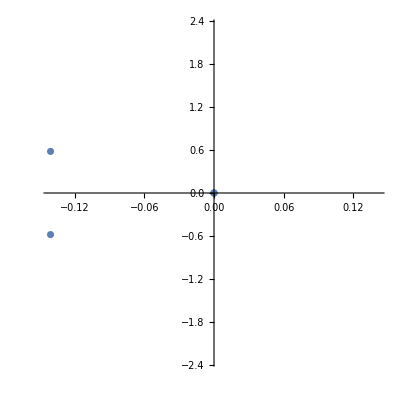

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@%415,AspectRatio->1]
```

```mathematica
gg.x^2-2x
```

{1,0,0,0,0,0,-1}

```mathematica
(GNC=Table[gnc[i,j],{i,n},{j,n}])//MatrixForm;
```

```mathematica
(vars2 = DeleteDuplicates[SparseArray[GNC]["NonzeroValues"]])//MatrixForm;
```

```mathematica
(WNC=h DiagonalMatrix[Table[9/8,{i,n}]]);
```

```mathematica
WNC[[1,1]]=3/8;WNC[[n,n]]=3/8;
```

```mathematica
WNC//MatrixForm
```

(3/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 9/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 9/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 9/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 9/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 9/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 3/8)

```mathematica
(*(soltmp=Solve[WNC.GNC+Transpose[WNC.GNC]==B,vars2][[1]]//Quiet)//MatrixForm
(GNCtmp=GNC/.soltmp)//MatrixForm
(vars2 = DeleteDuplicates[SparseArray[UpperTriangularize[GNCtmp,1]]["NonzeroValues"]])//MatrixForm;
solNC = Solve[{GNCtmp.c==0,GNCtmp.x==c,GNCtmp.x^2==2x(*,(GNCtmp.x^3)[[2;;3]]==(3 x^2)[[2;;3]]*)(*,WNC.GNC+Transpose[WNC.GNC]==B*)},vars2][[1]]
(GNC=GNCtmp/.solNC)//MatrixForm*)
```

```mathematica
solNC = Solve[{GNC.c==0,GNC.x==c,GNC.x^2==2x,WNC.GNC+Transpose[WNC.GNC]==B},vars2][[1]]
```

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
(GNC=GNC/.solNC)//MatrixForm
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧

```mathematica
GNC.c//MatrixForm
```

({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{1,1,1,1,1,1,1}

```mathematica
GNC.x-1//MatrixForm
```

-1+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,2,3,4,5,6}

```mathematica
GNC.x^2-2x//MatrixForm
```

(({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,4,9,16,25,36}
-2+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,4,9,16,25,36}
-4+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,4,9,16,25,36}
-6+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,4,9,16,25,36}
-8+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,4,9,16,25,36}
-10+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,4,9,16,25,36}
-12+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,4,9,16,25,36})

```mathematica
GNC.x^3-3 x^2//MatrixForm
```

(({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,8,27,64,125,216}
-3+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,8,27,64,125,216}
-12+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,8,27,64,125,216}
-27+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,8,27,64,125,216}
-48+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,8,27,64,125,216}
-75+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,8,27,64,125,216}
-108+({{gnc[1,1],gnc[1,2],gnc[1,3],gnc[1,4],gnc[1,5],gnc[1,6],gnc[1,7]},{gnc[2,1],gnc[2,2],gnc[2,3],gnc[2,4],gnc[2,5],gnc[2,6],gnc[2,7]},{gnc[3,1],gnc[3,2],gnc[3,3],gnc[3,4],gnc[3,5],gnc[3,6],gnc[3,7]},{gnc[4,1],gnc[4,2],gnc[4,3],gnc[4,4],gnc[4,5],gnc[4,6],gnc[4,7]},{gnc[5,1],gnc[5,2],gnc[5,3],gnc[5,4],gnc[5,5],gnc[5,6],gnc[5,7]},{gnc[6,1],gnc[6,2],gnc[6,3],gnc[6,4],gnc[6,5],gnc[6,6],gnc[6,7]},{gnc[7,1],gnc[7,2],gnc[7,3],gnc[7,4],gnc[7,5],gnc[7,6],gnc[7,7]}}/.{}⟦1⟧).{0,1,8,27,64,125,216})

```mathematica
(WLGR=h DiagonalMatrix[{2/9,-5/18(Sqrt[6](-2+3Sqrt[6]))/(-6+Sqrt[6]),5/18(Sqrt[6](2+3Sqrt[6]))/(6+Sqrt[6])}])//MatrixForm
```

(2/9 | 0 | 0
0 | -(5 (-2+3 √6))/(3 √6 (-6+√6)) | 0
0 | 0 | (5 (2+3 √6))/(3 √6 (6+√6)))

```mathematica
BLGR=DiagonalMatrix[{-1,0,1}];
```

```mathematica
(taT={{1},{0},{0}})//MatrixForm;
```

```mathematica
tbT={{1/3},{5/3(2Sqrt[6]-3)/(-6+Sqrt[6])},{5/3(2Sqrt[6]+3)/(6+Sqrt[6])}};
```

```mathematica
e1={{1,0,0}};
en={{0,0,1}};
(T=Transpose[e1].Transpose[taT]+Transpose[en].Transpose[tbT])//MatrixForm
```

(1 | 0 | 0
0 | 0 | 0
1/3 | (5 (-3+2 √6))/(3 (-6+√6)) | (5 (3+2 √6))/(3 (6+√6)))

```mathematica
(BLGR=Transpose[T].BLGR.T)//MatrixForm
```

(-8/9 | (5 (-3+2 √6))/(9 (-6+√6)) | (5 (3+2 √6))/(9 (6+√6))
(5 (-3+2 √6))/(9 (-6+√6)) | (25 (-3+2 √6)^2)/(9 (-6+√6)^2) | (25 (-3+2 √6) (3+2 √6))/(9 (-6+√6) (6+√6))
(5 (3+2 √6))/(9 (6+√6)) | (25 (-3+2 √6) (3+2 √6))/(9 (-6+√6) (6+√6)) | (25 (3+2 √6)^2)/(9 (6+√6)^2))

```mathematica
(GLGR=Table[lgr[i,j],{i,3},{j,3}])//MatrixForm;
```

```mathematica
(vars3 = DeleteDuplicates[SparseArray[GLGR]["NonzeroValues"]])//MatrixForm;
```

```mathematica
(*(sol3=Solve[WLGR.GLGR+Transpose[WLGR.GLGR]==BLGR,vars3][[1]])//MatrixForm*)
```

```mathematica
xlgr={-1,1/5-1/5 Sqrt[6],1/5+1/5 Sqrt[6]};
```

```mathematica
(solLGR=Solve[{GLGR.xlgr=={1,1,1},GLGR.xlgr^2==2xlgr,WLGR.GLGR+Transpose[WLGR.GLGR]==BLGR},vars3][[1]])//MatrixForm
```

(lgr[1,1]→-2
lgr[1,2]→(75 (7+2 √6))/((-6+√6)^2 (12+7 √6))
lgr[1,3]→(75 (-7+2 √6))/((6+√6)^2 (-12+7 √6))
lgr[2,1]→(20 (3+8 √6))/((-6+√6) (-2+3 √6) (12+7 √6))
lgr[2,2]→-(5 (-3+2 √6)^2)/(√6 (-6+√6) (-2+3 √6))
lgr[2,3]→-(125 (-3+2 √6))/((-6+√6) (-2+3 √6) (12+7 √6))
lgr[3,1]→(20 (-3+8 √6))/((6+√6) (2+3 √6) (-12+7 √6))
lgr[3,2]→-(125 (3+2 √6))/((6+√6) (2+3 √6) (-12+7 √6))
lgr[3,3]→(5 (3+2 √6)^2)/(√6 (6+√6) (2+3 √6)))

```mathematica
(GLGR=GLGR/.solLGR//Simplify)//MatrixForm
```

(-2 | 1+7/(2 √6) | 1-7/(2 √6)
-√(2/3) | 1/4 (4-√6) | -1+7/(2 √6)
√(2/3) | -1-7/(2 √6) | 1/4 (4+√6))

```mathematica
(*Gauss Chebyshev*)
```

```mathematica
pairs=ResourceFunction["ClenshawCurtisQuadratureWeights"][n,{-1,1}]
xi=pairs[[;;,1]];
wi=pairs[[;;,2]];
```

{{-1.,0.0285714},{-0.866025,0.253968},{-0.5,0.457143},{0.,0.520635},{0.5,0.457143},{0.866025,0.253968},{1.,0.0285714}}

```mathematica
(WGC=h DiagonalMatrix[wi])//MatrixForm
```

(0.0285714 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.253968 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.457143 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.520635 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.457143 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0.253968 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0.0285714)

```mathematica
(GGC=Table[ggc[i,j],{i,n},{j,n}])//MatrixForm;
```

```mathematica
(vars4= DeleteDuplicates[SparseArray[GGC]["NonzeroValues"]])//MatrixForm;
```

```mathematica
(solGC=Solve[{GGC.c==0,GGC.xi==c,GGC.xi^2==2xi,WGC.GGC+Transpose[WGC.GGC]==B},vars4][[1]]//Chop)//MatrixForm
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,1.,1.,1.,1.,1.,1.,0.},«47»,{0.0571429,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1.}} may contain significant numerical errors.

Part::partw: Part 1 of {} does not exist.

{}⟦1⟧

```mathematica
(*(GGC=GGC/.solGC)//MatrixForm*)
```

```mathematica
GGC.xi^3-3 xi^2
```

{-3.-1. ggc[1,1]-0.649519 ggc[1,2]-0.125 ggc[1,3]+0.125 ggc[1,5]+0.649519 ggc[1,6]+1. ggc[1,7],-2.25-1. ggc[2,1]-0.649519 ggc[2,2]-0.125 ggc[2,3]+0.125 ggc[2,5]+0.649519 ggc[2,6]+1. ggc[2,7],-0.75-1. ggc[3,1]-0.649519 ggc[3,2]-0.125 ggc[3,3]+0.125 ggc[3,5]+0.649519 ggc[3,6]+1. ggc[3,7],0.-1. ggc[4,1]-0.649519 ggc[4,2]-0.125 ggc[4,3]+0.125 ggc[4,5]+0.649519 ggc[4,6]+1. ggc[4,7],-0.75-1. ggc[5,1]-0.649519 ggc[5,2]-0.125 ggc[5,3]+0.125 ggc[5,5]+0.649519 ggc[5,6]+1. ggc[5,7],-2.25-1. ggc[6,1]-0.649519 ggc[6,2]-0.125 ggc[6,3]+0.125 ggc[6,5]+0.649519 ggc[6,6]+1. ggc[6,7],-3.-1. ggc[7,1]-0.649519 ggc[7,2]-0.125 ggc[7,3]+0.125 ggc[7,5]+0.649519 ggc[7,6]+1. ggc[7,7]}